```mathematica
(*Define Directions*)
xhat = {1,0};
yhat = {0,1};
thetahat = {1,0};
rhat = {0,1};

(*some nice helper functions*)
polarToCartesian[Θ_,R_]={R Cos[Θ],R Sin[Θ]};
rotToGrav[omega_,r_] = r*(omega^2);
cartesianToPolar[x_,y_] = {ArcTan[x,y],Sqrt[x^2 + y^2]};

(*Define functions for different projectile motions*)
(*arclength equation*)
arcLengthProjectileMotion[t_,v0_,ΘThrow_,Θinit_,r0_,omega_,R_] = Module[{
(*Define Local variables*)
refPointOnShip, startPointOnShip,projectilePath,initProjectileVelocity
},
refPointOnShip =  R{Cos[omega*t+Θinit],Sin[omega *t +Θinit]};
startPointOnShip =  r0{Cos[Θinit],Sin[Θinit]};
initProjectileVelocity = {v0 Cos[ΘThrow + Pi/2 +Θinit ],v0 Sin[ΘThrow + Pi/2 + Θinit]} +  r0*omega*{-Sin[Θinit],Cos[Θinit ]};
projectilePath = initProjectileVelocity * t +startPointOnShip;
{R*(Mod[ArcTan[xhat.projectilePath,yhat.projectilePath],2Pi]),R-Sqrt[projectilePath.projectilePath]}];



gravProjectileMotion [t_,v0_,Θ_,x0_,y0_,g_] = {
(*horizontal component*)
v0 t Cos[Θ]+x0,
(*vertical Component*)
-g/2*t^2 + v0 t Sin[Θ] + y0
};

arcLengthProjectileMotionL[t_,v0_,ΘThrow_,Θinit_,r0_,omega_,R_] ={-arcLengthProjectileMotion[t,v0,Pi-ΘThrow,Θinit,r0,omega,R].xhat,arcLengthProjectileMotion[t,v0,Pi-ΘThrow,Θinit,r0,omega,R].yhat}
```

{-R Mod[ArcTan[r0 Cos[Θinit]+t (-omega r0 Sin[Θinit]+v0 Sin[Θinit-ΘThrow]),t (omega r0 Cos[Θinit]-v0 Cos[Θinit-ΘThrow])+r0 Sin[Θinit]],2 π],R-√((t (omega r0 Cos[Θinit]-v0 Cos[Θinit-ΘThrow])+r0 Sin[Θinit])^2+(r0 Cos[Θinit]+t (-omega r0 Sin[Θinit]+v0 Sin[Θinit-ΘThrow]))^2)}

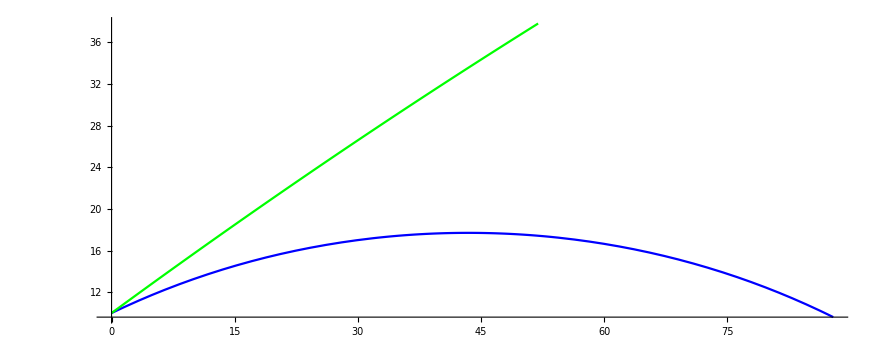

```mathematica
ArcLengthPlotRight = ParametricPlot[arcLengthProjectileMotion[t,3,Pi/6,0,100,.01,110],{t,0,20},PlotStyle->Blue];
ArcLengthPlotLeft = ParametricPlot[arcLengthProjectileMotionL[t,3,Pi/6,0,100,.01,110],{t,0,20},PlotStyle->Red];
equivGrav = rotToGrav[.01,110];
gravProjectileMotionPlot = ParametricPlot[gravProjectileMotion[t,3,Pi/6,0,10,equivGrav],{t,0,20},PlotStyle->Green];
Show[ArcLengthPlotRight,gravProjectileMotionPlot,PlotRange->All]
```

```mathematica
.
```

```mathematica
inertialPlotRight = ParametricPlot[Module[{arclen ,theta,radius},
arclen = arcLengthProjectileMotion[t,3,Pi/6,-Pi/2,100,.01,110];
theta =( arclen.thetahat)/110 ;
radius = -1*arclen.rhat + 110;
{radius Cos[theta],radius Sin[theta]
}],{t,0,40}];
inertialPlotLeft = ParametricPlot[Module[{arclen ,theta,radius},
arclen = arcLengthProjectileMotion[t,3,5Pi/6,-Pi/2,100,.01,110];
theta =( arclen.thetahat)/110 ;
radius = -1*arclen.rhat + 110;
{radius Cos[theta],radius Sin[theta]
}],{t,0,40}];
```

```mathematica
Mod[ArcTan[1,0],2Pi]
```

0

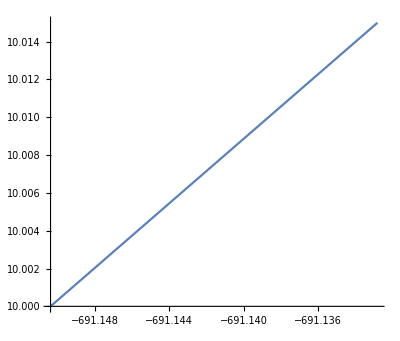

```mathematica
ParametricPlot[arcLengthProjectileMotionL[t,3,Pi/6,0,100,.01,110],{t,0,.01}]
```

```mathematica
0
```

0

```mathematica
{-arcLengthProjectileMotion[t,3,5Pi/6,0,100,.01,110].xhat,arcLengthProjectileMotion[t,3,5Pi/6,0,100,.01,110].yhat}
```

{-110 Mod[ArcTan[100-1.5 t,-1.59808 t],2 π],110-√((100-1.5 t)^2+2.55385 t^2)}

```mathematica
arcLengthProjectileMotionL[0,3,Pi/6,0,100,.01,110]
```

{0.,10.}

```mathematica
Tang[t_]=D[arcLengthProjectileMotion[t,3,Pi/6,0,100,.01,110],t]
```

{110 ((3.59808 (100-1.5 t))/((100-1.5 t)^2+12.9462 t^2)+(5.39711 t)/((100-1.5 t)^2+12.9462 t^2)-((3.59808 (100-1.5 t))/((100-1.5 t)^2+12.9462 t^2)+(5.39711 t)/((100-1.5 t)^2+12.9462 t^2)) (Piecewise[{{0, ArcTan[100-1.5 t,3.59808 t]/(2 π)>Floor[ArcTan[100-1.5 t,3.59808 t]/(2 π)]}, {Indeterminate, True}}])),-(-3. (100-1.5 t)+25.8923 t)/(2 √((100-1.5 t)^2+12.9462 t^2))}

```mathematica
Tang[0]
```

{Indeterminate,1.5}

## Taylor Series Expansion

```mathematica
verticalFormula = arcLengthProjectileMotion[t,V0,thetaThrow,-Pi/2,r,Sqrt[g/R],R].{0,1} //FullSimplify;
horizontalFormula =  arcLengthProjectileMotion[t,V0,thetaThrow,-Pi/2,R-h,omega,R].{1,0} //FullSimplify;
Series[verticalFormula,{t,0,3}]
```

(-√(r^2)+R)+(√(r^2) V0 Sin[thetaThrow] t)/r+((-g r^2-2 r √(g/R) R V0 Cos[thetaThrow]-R V0^2 Cos[thetaThrow]^2) t^2)/(2 √(r^2) R)-(((g r^2 V0+2 r √(g/R) R V0^2 Cos[thetaThrow]+R V0^3 Cos[thetaThrow]^2) Sin[thetaThrow]) t^3)/(2 (r √(r^2) R))+O[t]^4

```mathematica
(-√((h-R)^2)+R)+((-h V0 Sin[thetaThrow]+R V0 Sin[thetaThrow]) t)/(√((h-R)^2))-((g h^2-2 g h R+g R^2-2 h √(g/R) R V0 Cos[thetaThrow]+2 √(g/R) R^2 V0 Cos[thetaThrow]+R V0^2 Cos[thetaThrow]^2) t^2)/(2 (√((h-R)^2) R))+(V0 (g h^2-2 g h R+g R^2-2 h √(g/R) R V0 Cos[thetaThrow]+2 √(g/R) R^2 V0 Cos[thetaThrow]+R V0^2 Cos[thetaThrow]^2) Sin[thetaThrow] t^3)/(2 (h-R) √((h-R)^2) R)+O[t]^4
```

(-√((h-R)^2)+R)+((-h V0 Sin[thetaThrow]+R V0 Sin[thetaThrow]) t)/(√((h-R)^2))-((g h^2-2 g h R+g R^2-2 h √(g/R) R V0 Cos[thetaThrow]+2 √(g/R) R^2 V0 Cos[thetaThrow]+R V0^2 Cos[thetaThrow]^2) t^2)/(2 (√((h-R)^2) R))+(V0 (g h^2-2 g h R+g R^2-2 h √(g/R) R V0 Cos[thetaThrow]+2 √(g/R) R^2 V0 Cos[thetaThrow]+R V0^2 Cos[thetaThrow]^2) Sin[thetaThrow] t^3)/(2 (h-R) √((h-R)^2) R)+O[t]^4

```mathematica
CoefficientList[%,t]
```

{{-√(r^2)+R},{(√(r^2) V0 Sin[thetaThrow])/r},{(-g r^2-2 r √(g/R) R V0 Cos[thetaThrow]-R V0^2 Cos[thetaThrow]^2)/(2 √(r^2) R)},{-((g r^2 V0+2 r √(g/R) R V0^2 Cos[thetaThrow]+R V0^3 Cos[thetaThrow]^2) Sin[thetaThrow])/(2 r √(r^2) R)}}

(-√((h-R)^2)+R)+((-h V0 Sin[thetaThrow]+R V0 Sin[thetaThrow]) t)/(√((h-R)^2))-((g h^2-2 g h R+g R^2-2 h √(g/R) R V0 Cos[thetaThrow]+2 √(g/R) R^2 V0 Cos[thetaThrow]+R V0^2 Cos[thetaThrow]^2) t^2)/(2 (√((h-R)^2) R))+(V0 (g h^2-2 g h R+g R^2-2 h √(g/R) R V0 Cos[thetaThrow]+2 √(g/R) R^2 V0 Cos[thetaThrow]+R V0^2 Cos[thetaThrow]^2) Sin[thetaThrow] t^3)/(2 (h-R) √((h-R)^2) R)+O[t]^4

```mathematica
(-g r^2-2 r √(g/R) R V0 Cos[thetaThrow]-R V0^2 Cos[thetaThrow]^2)/(2 √(r^2) R)
```

(-g r^2-2 r √(g/R) R V0 Cos[thetaThrow]-R V0^2 Cos[thetaThrow]^2)/(2 √(r^2) R)